With a Cap in the integration boundary (?, not sure anymore)

```mathematica
Exit[]
```

```mathematica
D[Max[0,(1-Exp[-a xx[w t,t]-s])Exp[-w^2/2]],a]
```

Piecewise[{{ⅇ^(-a (-1+ⅇ^((-1/2+mpr) t^2+t w))-s-w^2/2) (-1+ⅇ^(a (-1+ⅇ^((-1/2+mpr) t^2+t w))+s)) (1-ⅇ^((-1/2+mpr) t^2+t w))+ⅇ^(-w^2/2) (-1+ⅇ^((-1/2+mpr) t^2+t w)), -ⅇ^(-w^2/2)+ⅇ^(-a (-1+ⅇ^((-1/2+mpr) t^2+t w))-s-w^2/2)<0}, {0, True}}]

```mathematica
$Assumptions=s>0&&t>0&&b>0&&μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
xx[W_,t_]:=Exp[  W+(mpr-1/2)t^2]-1;
w1[a_,t_,s_]:=If[a>s,(t^2-2 mpr t^2+2 Log[(a-s)/a])/(2 t),-∞];
w2[a_,t_,s_]:=If[a≤ 0,(t^2-2 mpr t^2+2 Log[(a-s)/a])/(2 t),∞];
```

```mathematica
mpr=.;Simplify[a xx[w1[a,t,s] t,t]+s≥ 0]
Simplify[a xx[w2[a,t,s] t,t]+s]
```

True

Piecewise[{{s+a ∞, a>0}, {0, True}}]

```mathematica
g[a_,t_,s_]:=√(π/2) (Erf[w2[a,t,s]/(√2)]-Erf[w1[a,t,s]/(√2)])- NIntegrate[Exp[-a xx[w t,t]-s-w^2/2],{w,w1[a,t,s],w2[a,t,s]}];
gs[a_,t_,s_]:=NIntegrate[xx[w t,t]Exp[-a xx[w t,t]-s-w^2/2],{w,w1[a,t,s],w2[a,t,s]}];
g2[a_,t_,s_]:=NIntegrate[Max[0,(1-Exp[-a xx[w t,t]-s])Exp[-w^2/2]],{w,-∞,∞}];
as[t_,s_]:=Quiet[FindRoot[gs[a,t,s]==0,{a,-1,1}][[1,2]]]
```

```mathematica
as[1,1.]
```

0.277783

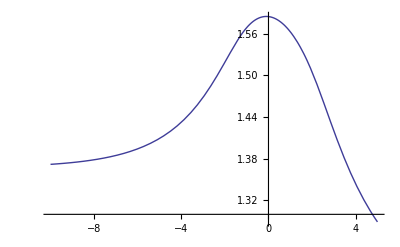

```mathematica
mpr=-.1;Plot[ {g[a,.2,1]},{a,-10,5}]
```

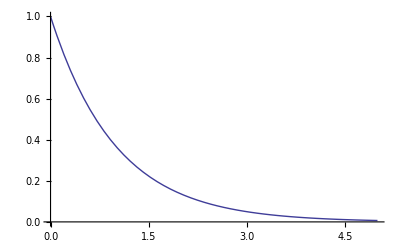

```mathematica
Plot[Exp[-x],{x,0,5}]
```